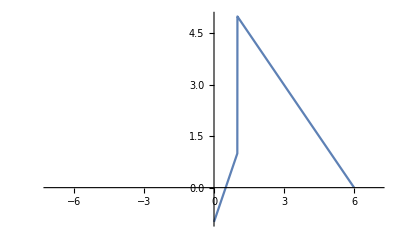

Разложим функцию f в ряд по косинусам.

Также представим y в виде ряда по косинусам, используя представление f рядом в правоц части, найдём коэффициенты ряда Фурье для y

Коэффициенты разложения для f

{{1/6 ((3 (6 (2+√3)-5 π))/π^2-6/π-(3 (6 (2+√3)+7 π))/π^2),0},{1/6 (-(3 √3)/π+(9-21 √3 π)/(2 π^2)-(3 (3+5 √3 π))/(2 π^2)),0},{1/6 ((4-10 π)/π^2-4/π-(2 (2+7 π))/π^2),0},{1/6 (-(3 √3)/(2 π)+(27-42 √3 π)/(8 π^2)-(3 (9+10 √3 π))/(8 π^2)),0},{1/6 (-6/(5 π)-(3 (6 (-2+√3)+25 π))/(25 π^2)-(3 (12-6 √3+35 π))/(25 π^2)),0},{0,0},{1/6 (6/(7 π)+(3 (12-6 √3+35 π))/(49 π^2)+(3 (6 (-2+√3)+49 π))/(49 π^2)),0},{1/6 ((3 √3)/(4 π)+(3 (-9+20 √3 π))/(32 π^2)+(3 (9+28 √3 π))/(32 π^2)),0},{1/6 (4/(3 π)+(2 (-2+21 π))/(9 π^2)+(4+30 π)/(9 π^2)),0},{1/6 ((3 √3)/(5 π)+(3 (-3+25 √3 π))/(50 π^2)+(3 (3+35 √3 π))/(50 π^2)),0}}

1/6 ((3 (6 (2+√3)-5 π))/π^2-6/π-(3 (6 (2+√3)+7 π))/π^2) | 0
1/6 (-(3 √3)/π+(9-21 √3 π)/(2 π^2)-(3 (3+5 √3 π))/(2 π^2)) | 0
1/6 ((4-10 π)/π^2-4/π-(2 (2+7 π))/π^2) | 0
1/6 (-(3 √3)/(2 π)+(27-42 √3 π)/(8 π^2)-(3 (9+10 √3 π))/(8 π^2)) | 0
1/6 (-6/(5 π)-(3 (6 (-2+√3)+25 π))/(25 π^2)-(3 (12-6 √3+35 π))/(25 π^2)) | 0
0 | 0
1/6 (6/(7 π)+(3 (12-6 √3+35 π))/(49 π^2)+(3 (6 (-2+√3)+49 π))/(49 π^2)) | 0
1/6 ((3 √3)/(4 π)+(3 (-9+20 √3 π))/(32 π^2)+(3 (9+28 √3 π))/(32 π^2)) | 0
1/6 (4/(3 π)+(2 (-2+21 π))/(9 π^2)+(4+30 π)/(9 π^2)) | 0
1/6 ((3 √3)/(5 π)+(3 (-3+25 √3 π))/(50 π^2)+(3 (3+35 √3 π))/(50 π^2)) | 0

Коэффициенты разложения для y

{{{{ay→7/π^3}},0},{{{ay→(7 √3)/(8 π^3)}},0},{{{ay→14/(27 π^3)}},0},{{{ay→(7 √3)/(64 π^3)}},0},{{{ay→7/(125 π^3)}},0},{{{ay→0}},0},{{{ay→-1/(49 π^3)}},0},{{{ay→-(7 √3)/(512 π^3)}},0},{{{ay→-14/(729 π^3)}},0},{{{ay→-(7 √3)/(1000 π^3)}},0}}

ay→7/π^3 | 0
ay→(7 √3)/(8 π^3) | 0
ay→14/(27 π^3) | 0
ay→(7 √3)/(64 π^3) | 0
ay→7/(125 π^3) | 0
ay→0 | 0
ay→-1/(49 π^3) | 0
ay→-(7 √3)/(512 π^3) | 0
ay→-14/(729 π^3) | 0
ay→-(7 √3)/(1000 π^3) | 0

{{x→38.6667}}

Решение y(t) = a0/2 + ∑_(k = 1)^∞ (2 (7 Sin[FractionBox[k π, 6]] - 6 Sin[k π]))/k^3*Cos[k*Pi*t/6]:

{{-7/3+(x→38.6667)/2}}

```mathematica
Clear[f]
f[t_]:=2*t-1/;0≤t≤1
f[t_]:=6-t/;1<t≤6
Plot[f[t],{t,-7,7}]
Clear[a,L]
L = 6;
Text["Разложим функцию f в ряд по косинусам."]
a[0] := 2/L*(NIntegrate[2t-1,{t,-1,1}]+NIntegrate[6-t,{t,1,6}]+NIntegrate[6-t,{t,-6,-1}]);
a[k_]:=((1/6)*(Integrate[(2t-1)Cos[π*k*t/6],{t,-1,1}]+Integrate[(6-t)Cos[π*k*t/6],{t,1,6}]+Integrate[(6-t)Cos[π*k*t/6],{t,-6,-1}]));
Text["Также представим y в виде ряда по косинусам, используя представление f рядом в правоц части, найдём коэффициенты ряда Фурье для y"]
a1[0]:=Solve[x/2==a[0],x]
a1[k_]:=Solve[ay*(-k^2*Pi^2)==a[k],ay]
Print["Коэффициенты разложения для f"]
coeffs = Table[{a[i],0},{i,1,10}]
TableForm[coeffs]
Print["Коэффициенты разложения для y"]
coeffs1= Table[{a1[i],0},{i,1,10}]
TableForm[coeffs1]
a1[0]
Text["Решение y(t) = a0/2 + ∑_(k = 1)^∞ (2 (7 Sin[FractionBox[k π, 6]] - 6 Sin[k π]))/k^3*Cos[k*Pi*t/6]: "]
Print[a1[0]/2+Sum[a[k]*Cos[k*Pi/6],{k,1,Infinity}]]
```